```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Analysis of KS Hamiltonian in the NBO basis

The following analysis is performed on bent and planar anthracene as calculated in Gaussian16 using the functional PBE with a cc-pVDZ basis set, NOT augmented with diffuse functions to prevent losing linearly dependent eigenvectors needed to analyze the solution.

### Contents

Import Data from CSV
Re-label Atoms
	Set Scheme
Decoupling  and  with Block Diagonalisation
Symmetry Analysis

## Definitions

Output from Gaussian is generally in atomic units . Elements of the KS matrix are in units of Hartree and are printed to the 4th digit after the decimal place . To help with conversions, we define the following function

```mathematica
H2eV[a_]:=QuantityMagnitude[UnitConvert[Quantity[a,"HartreeEnergy"],"Electronvolts"]];
```

Using this function, we see that changes in the last decimal place represent changes of 0.002 eV

```mathematica
H2eV[0.0001]
```

0.00272114

### Defining a Color Function

We define a color function here for later use. This is a symmetric scheme that places the colours from Kori’s colour pallette evenly along a line from negative the maximum to the maximum, with white in the middle.

```mathematica
rgb[r_,g_,b_]:=RGBColor[r/255,g/255,b/255];
symmetricCF[max_]:=(step=max/5;Function[{y},Function[x,Blend[{{-max,rgb[25,65,87]},{-max+step,rgb[45,92,136]},{-max+2*step,rgb[81,148,153]},{-max+3*step,rgb[134,199,186]},{-max+4*step,rgb[198,229,223]},{0,rgb[255,255,255]},{max-step*4,rgb[223,182,84]},{max-3*step,rgb[210,130,78]},{max-step*2,rgb[196,69,58]},{max-step,rgb[160,48,35]},{max,rgb[98,30,66]}},x]][y]])
```

### Defining a Nice Matrix Plot Function

```mathematica
prettyPlot[matrix_,cf_,lowerBarBound_,upperBarBound_]:=MatrixPlot[matrix,ImageSize->Medium,ColorFunction->cf,ColorFunctionScaling->False,PlotTheme->"Scientific",FrameTicks->{{All,False},{False,All}},FrameTicksStyle->18,PlotLegends->BarLegend[{cf,{lowerBarBound,upperBarBound}},LegendMarkerSize->300,LabelStyle->{FontFamily->"Times",FontSize->14,FontWeight->Bold}]];
```

### Defining a Nice Energy Level Plot Function

```mathematica
makeLines[points_,offset_]:=Table[{Mod[Mod[i,2]+j,2]+offset,points[[i]]},{i,1,Length[points]},{j,0,1}];
spectrum[energyLevels_,reference_,range_]:=ListLinePlot[energyLevels-reference,
Frame->{{True,False},{False,False}},PlotRange->range];
```

## Sanity Check Info

Using the eigenvalues from Gaussian, the HOMO - LUMO gap is

```mathematica
(* planar *) H2eV[-0.09477+0.17174]
(* bent *) H2eV[-0.09297+0.17682]
(* blueshift *)H2eV[-0.09297+0.17682]-H2eV[-0.09477+0.17174]
```

2.09446

2.28167

0.187214

## Set Location of Data Files

```mathematica
SetDirectory["/Users/sina/Library/CloudStorage/OneDrive-UCB-O365/Projects/MoleculesAttachedToSi/anthracene_ESFG_manuscript/data"];
```

## Import Data from CSVs and Re-arrange

### Planar Anthracene

The Fock matrix of the planar anthracene is stored as “pbe_nbo_planar_fock.csv”. It is pulled in and temporarily labeled data. The eigenvalues of the full matrix are pulled to check against the values reported by Gaussian. They are within 0.003 eV of each other.

```mathematica
data=Import["./pbe_nbo_planar_fock.csv"];
{eigE,eigV}=Eigensystem[data[[2;;,8;;]]];Sort[eigE[[;;]]];
fullHLgapPlanar=H2eV[%[[48]]-%[[47]]]
```

2.09429

Using the column that labels the states as ‘pz’ or ‘sp2’, we sort the matrix into chunks with the following form (p_z | V
V^T | sp^2) , ignoring the core s orbitals and the high energy Rydberg states. We print the final ordering as a sanity check and ensure that the phase on the orbitals will be consistent between our calculations.

(pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 1 | 2 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 12 | 13 | 15 | 17 | 20 | 22 | 24 | 221 | 222 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 232 | 233 | 235 | 237 | 240 | 242 | 244 | 3 | 11 | 14 | 16 | 18 | 19 | 21 | 23 | 25 | 26 | 223 | 231 | 234 | 236 | 238 | 239 | 241 | 243 | 245 | 246
C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C
1(lp*) | 2(lp) | 3(lp) | 4(lp) | 5(lp*) | 6(lp) | 7(lp*) | 8(lp) | 9(lp) | 10(lp*) | 11(lp*) | 12(lp) | 13(lp*) | 14(lp*) | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 7 | 8 | 9 | 11 | 12 | 13 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 7 | 8 | 9 | 11 | 12 | 13 | 1 | 5 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 1 | 5 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
 |  |  |  |  |  |  |  |  |  |  |  |  |  | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
 |  |  |  |  |  |  |  |  |  |  |  |  |  | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 | 3 | 4 | 11 | 6 | 7 | 5 | 14 | 6 | 10 | 8 | 9 | 10 | 12 | 13 | 14 | 2* | 3* | 4* | 11* | 6* | 7* | 5* | 14* | 6* | 10* | 8* | 9* | 10* | 12* | 13* | 14* | 19 | 24 | 22 | 23 | 21 | 20 | 15 | 16 | 17 | 18 | 19* | 24* | 22* | 23* | 21* | 20* | 15* | 16* | 17* | 18*)

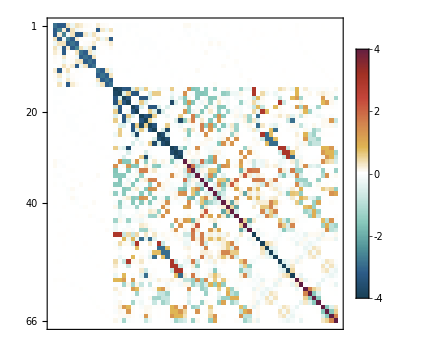

```mathematica
oA=Reverse[Reverse[Ordering[data[[;;,1]]]][[;;80]]];
o=Join[oA[[21;;21+14-1]],oA[[-32;;]],oA[[1;;20]]];(*,oA[[21+14;;-33]]];*)
Transpose[data[[o,1;;7]]]//MatrixForm
planarMatrix=data[[o,o+6]];
planarMatrix[[;;,26]]=-planarMatrix[[;;,26]];planarMatrix[[26,;;]]=-planarMatrix[[26,;;]];
planarMatrix[[;;,42]]=-planarMatrix[[;;,42]];planarMatrix[[42,;;]]=-planarMatrix[[42,;;]];
prettyPlot[H2eV[planarMatrix],symmetricCF[4],-4,4]
```

### Bent Anthracene

The above code can largely be copy pasted with some tweaks here and there to perform the same operations on the Fock matrix of the bent anthracene. For example, the name of the data file is “pbe_nbo_bent_fock.csv”, a different orbital needs to have its phase flipped, and names are changed on variables.

```mathematica
data=Import["./pbe_nbo_bent_fock.csv"];
{eigE,eigV}=Eigensystem[data[[2;;,8;;]]];Sort[eigE[[;;]]];
fullHLgapBent=H2eV[%[[48]]-%[[47]]]
```

2.2842

(pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | pz | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | sp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2 | CHsp2
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 1 | 2 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 12 | 13 | 15 | 17 | 20 | 22 | 24 | 221 | 222 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 232 | 233 | 235 | 237 | 240 | 242 | 244 | 3 | 11 | 14 | 16 | 18 | 19 | 21 | 23 | 25 | 26 | 223 | 231 | 234 | 236 | 238 | 239 | 241 | 243 | 245 | 246
C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C
1(lp*) | 2(lp) | 3(lp) | 4(lp) | 5(lp*) | 6(lp) | 7(lp*) | 8(lp) | 9(lp*) | 10(lp*) | 11(lp*) | 12(lp) | 13(lp) | 14(lp*) | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 7 | 8 | 9 | 11 | 12 | 13 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 7 | 8 | 9 | 11 | 12 | 13 | 1 | 5 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 1 | 5 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
 |  |  |  |  |  |  |  |  |  |  |  |  |  | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
 |  |  |  |  |  |  |  |  |  |  |  |  |  | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | C | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H | H
 |  |  |  |  |  |  |  |  |  |  |  |  |  | 2 | 3 | 4 | 11 | 6 | 7 | 5 | 14 | 6 | 10 | 8 | 9 | 10 | 12 | 13 | 14 | 2* | 3* | 4* | 11* | 6* | 7* | 5* | 14* | 6* | 10* | 8* | 9* | 10* | 12* | 13* | 14* | 19 | 24 | 22 | 23 | 21 | 20 | 15 | 16 | 17 | 18 | 19* | 24* | 22* | 23* | 21* | 20* | 15* | 16* | 17* | 18*)

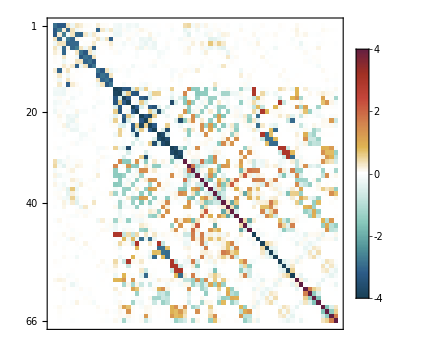

```mathematica
oA=Reverse[Reverse[Ordering[data[[;;,1]]]][[;;80]]];
o=Join[oA[[21;;21+14-1]],oA[[-32;;]],oA[[1;;20]]];(*,oA[[21+14;;-33]]];*)
Transpose[data[[o,1;;7]]]//MatrixForm
bentMatrix=data[[o,o+6]];
bentMatrix[[;;,5]]=-bentMatrix[[;;,5]];bentMatrix[[5,;;]]=-bentMatrix[[5,;;]];
prettyPlot[H2eV[bentMatrix],symmetricCF[4],-4,4]
```

## Relabeling Scheme

The original numbering scheme of the atoms was just their order in the XYZ file, depicted in the below figure.

```mathematica
Import["/Users/sina/Library/CloudStorage/OneDrive-UCB-O365/Projects/MoleculesAttachedToSi/anthracene_ESFG_manuscript/possible_figures/default_labeling_reference.png"]
```

-Graphics-

We want to relabel the atoms in a way that makes sense, focusing on the carbon atoms. A permutation of the above scheme that minimizes jumps between bonded carbons is the following

```mathematica
singleLoopPzLabeling={11,12,13,14,4,5,6,10,9,8,7,3,1,2};
```

A couple permutations that group the anthracene in a way that makes the molecular junction analogy more obvious are

```mathematica
junctionPzLabeling={7,8,9,10,1,3,6,5,4,2,11,12,13,14};
junctionPzLabeling2={7,8,9,10,6,3,4,2,11,12,13,14,1,5};
junctionPzLabeling3={3,7,8,9,10,6,5,1,2,11,12,13,14,4};
```

The sp2 blocks take a bit more care as we have the subsets of bonding and anti-bonding orbitals as well as C-C and C-H bonds. For the C-C bonds, we can define similar labeling schemes and the antibonding orbitals can be taken into account by a shift of 16 on the below indexing. For C-H bonds, only a cycle around the anthracene makes sense, but cyclic permutations would be valid. We refer to the labeling from the CSV file for the meaning of the numbers

```mathematica
singleLoopSP2Labeling={14,15,16,8,7,9,10,13,12,11,6,2,1,4,3,5};
junctionSP2Labeling={6,11,12,13,10,2,5,9,7,3,1,4,14,15,16,8};
```

We build a matrix that will perform the given permutations with the following functions

```mathematica
swapPz[scheme_]:=(t=ConstantArray[0,{14,14}];Do[t[[i,scheme[[i]]]]=1,{i,1,14}];t);
swapSP2[scheme_]:=(t=ConstantArray[0,{32,32}];list=Join[scheme,scheme+16];Do[t[[i,list[[i]]]]=1,{i,1,32}];t);
swapCHSP2=(t=ConstantArray[0,{20,20}];list=Join[{7,8,9,10,2,6,5,4,3,1},{7,8,9,10,2,6,5,4,3,1}+10];
Do[t[[i,list[[i]]]]=1,{i,1,20}];t);
```

#### Example of the permutations on the pz block of planar and bent anthracene

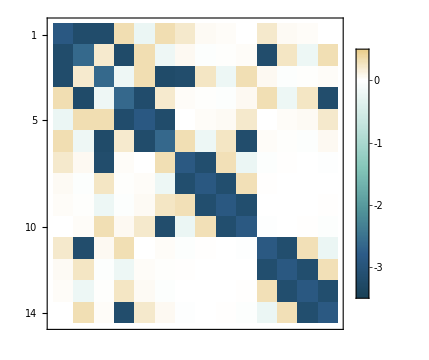
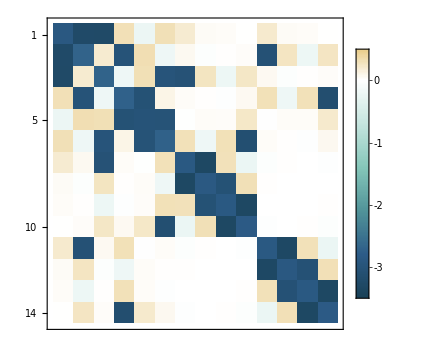
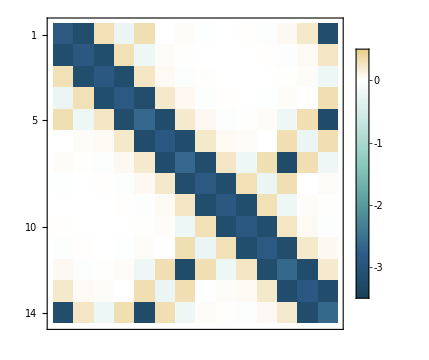
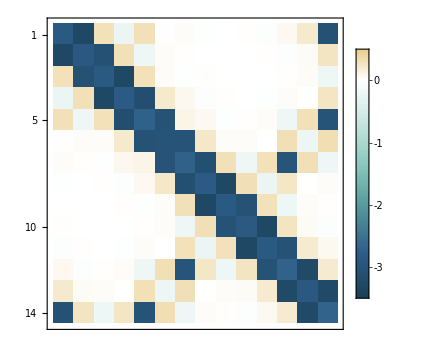
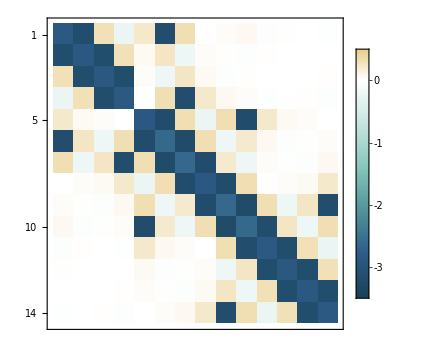
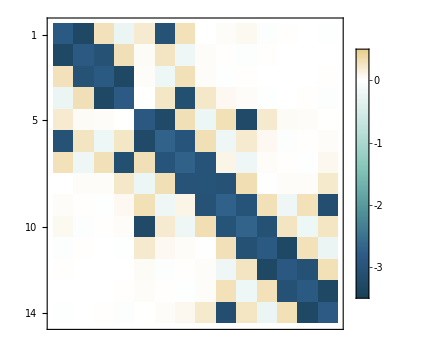
|  Block of Planar Anthracene |  Block of Bent Anthracene
No Permutations | -Graphics- | -Graphics-
singleLoop Scheme | -Graphics- | -Graphics-
junction Scheme | -Graphics- | -Graphics-

```mathematica
Grid[{{""," Block of Planar Anthracene"," Block of Bent Anthracene"},{"No Permutations",prettyPlot[H2eV[planarMatrix[[;;14,;;14]]],symmetricCF[3.5],-3.5,0.5],prettyPlot[H2eV[bentMatrix[[;;14,;;14]]],symmetricCF[3.5],-3.5,0.5]},{"singleLoop Scheme",prettyPlot[H2eV[swapPz[singleLoopPzLabeling].planarMatrix[[;;14,;;14]].Transpose[swapPz[singleLoopPzLabeling]]],symmetricCF[3.5],-3.5,0.5]
,prettyPlot[H2eV[swapPz[singleLoopPzLabeling].bentMatrix[[;;14,;;14]].Transpose[swapPz[singleLoopPzLabeling]]],symmetricCF[3.5],-3.5,0.5]},{"junction Scheme",prettyPlot[H2eV[swapPz[junctionPzLabeling].planarMatrix[[;;14,;;14]].Transpose[swapPz[junctionPzLabeling]]],symmetricCF[3.5],-3.5,0.5],prettyPlot[H2eV[swapPz[junctionPzLabeling].bentMatrix[[;;14,;;14]].Transpose[swapPz[junctionPzLabeling]]],symmetricCF[3.5],-3.5,0.5]}}]
```

### Full Permutation Matrix

The matrix that permutes the full submatrix is given by

```mathematica
Upermutation[scheme1_,scheme2_]:=BlockDiagonalMatrix[{swapPz[scheme1],swapSP2[scheme2],swapCHSP2}];
```

### Redefinition of matrices using desired scheme

```mathematica
s1=junctionPzLabeling3;s2=junctionSP2Labeling;
planarMatrix=Upermutation[s1,s2].planarMatrix.Transpose[Upermutation[s1,s2]];
bentMatrix=Upermutation[s1,s2].bentMatrix.Transpose[Upermutation[s1,s2]];
```

### Build the Connectivity Matrix

The list of connected atoms in the undisturbed labeling scheme is as follows

```mathematica
connectionList={{1,2},{1,3},{2,4},{2,11},{3,6},{3,7},{4,5},{4,14},{5,6},{6,10},{7,8},{8,9},{9,10},{11,12},{12,13},{13,14}};
```

From this we can build a connectivity matrix that has zeros if two atoms are not neighbors and ones where the two atoms are neighbors

```mathematica
connectivityMatrix=ConstantArray[0,{14,14}];Do[connectivityMatrix[[connectionList[[i,1]],connectionList[[i,2]]]]=1,{i,1,16}];connectivityMatrix=connectivityMatrix+Transpose[connectivityMatrix];
```

This matrix can likewise be rotated based on the desired labeling scheme

```mathematica
connectivityMatrix=swapPz[s1].connectivityMatrix.Transpose[swapPz[s1]];
```

## Block Diagonalisation of Hermitian Matrices (Cederbaum)

In the 1989 paper by L.S. Cederbaum, it is shown that the unitary matrix that will block diagonalize a Hermitian matrix, while preserving the original matrix as much as possible, is given by  where  is the matrix coefficient that satisfies  and  is the block diagonal part of . For the Fock matrix of the bent anthracene, we decouple the  and  blocks using this method

```mathematica
{Λ,Cbent}=Eigensystem[bentMatrix];
(* find the indices for the eigenvalues of the pz block within the full array of eigenvalues*)
eigPzEBent=Sort[Eigenvalues[bentMatrix[[;;14,;;14]]]];
pzBlockE = Flatten[Table[Position[Λ,(ArrayFlatten[Table[Nearest[Λ,eigPzEBent[[i]]],{i,1,14}],1])[[i]]],{i,1,14}]];
```

We want to obtain the order of eigenvalues (and therefore eigenvectors) that preserves the pz and sp2 blocks when applying the coefficient matrix  to the full matrix

```mathematica
order=Join[pzBlockE,Complement[Table[i,{i,1,66}],pzBlockE]];
Cbent=Transpose[Cbent[[order,;;]]]; (* transpose, to match the definition in Cederbaum's paper *) 
(* uncomment to verify this yields the correct arrangment of eigenvalues*)
(*MatrixForm[Chop[Transpose[Cbent].bentMatrix.Cbent]]*)
```

Defining the block diagonal parts of

```mathematica
CBD11=Cbent[[;;14,;;14]];
CBD22=Cbent[[15;;,15;;]];
CBD=BlockDiagonalMatrix[{CBD11,CBD22}];
```

To avoid issues if  is near singular, we compute  using SVD. In short, we write , that the inverse square root becomes

```mathematica
{U,Σ,Vt}=SingularValueDecomposition[CBD];
```

Then the unitary matrix  is

```mathematica
T=Cbent.Transpose[CBD].(U.Inverse[Σ].Transpose[U]);
```

We can check the Euclidean distance between this matrix and unity to get a sense of how perturbed our original Hamiltonian is after block diagonalization

```mathematica
EuclideanDistance[IdentityMatrix[Length[T]],T]/Length[T]
```

0.00215203

And the block diagonal form of the Fock matrix in the bent anthracene is

```mathematica
bentMatrixBD=Chop[Transpose[T].bentMatrix.T];
```

The difference with the original pz block is

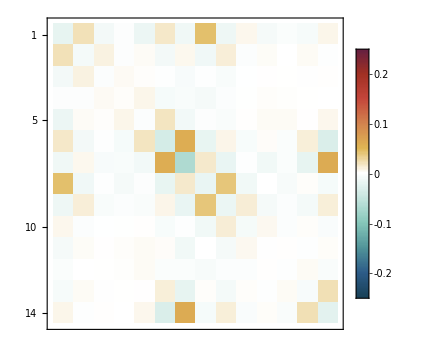

```mathematica
prettyPlot[H2eV[bentMatrixBD[[;;14,;;14]]-bentMatrix[[;;14,;;14]]],symmetricCF[0.25],-0.25,0.25]
```

And the difference with the planar matrix is

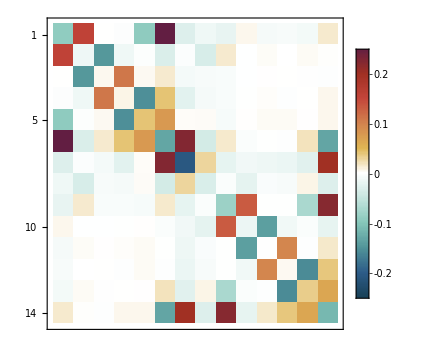

```mathematica
prettyPlot[H2eV[bentMatrixBD[[;;14,;;14]]-planarMatrix[[;;14,;;14]]],symmetricCF[0.25],-0.25,0.25]
```

We define this difference as the perturbation  on the original pz Hamiltonian

```mathematica
H0 = planarMatrix[[;;14,;;14]];
V=bentMatrixBD[[;;14,;;14]]-planarMatrix[[;;14,;;14]];
```

## Symmetry Analysis

First, some useful functions for creating matrices

```mathematica
myDiag[list_,n_]:=DiagonalMatrix[list,n]+DiagonalMatrix[list,-n];
(*Nice way to add elements symmetrically to a matrix *)
addElement[size_,a_,n1_,n2_]:=(t=0*IdentityMatrix[size];t[[n1,n2]]=a;t[[n2,n1]]=a;t)
```

For reference, some default values from standard Huckel benzene parameters in eV

```mathematica
αdef=-11.4;
βdef=-2.45;
```

And some variable assumptions that will help in simplifications

```mathematica
$Assumptions={α∈ Reals,β∈Reals}
```

{α∈ℝ,β∈ℝ}

### Symmetry operation matrices

Cn refers to rotations about the z - axis of 360/n degrees
sigma are reflections about the horizontal (h) plane, the vertical (v) plane through the carbon atoms, and the diagonal (d) plane through the bond midpoints
i is inversion through the center of the molecule
Sn refers to improper rotations, that is Cn rotation followed by a horizontal reflection

D  has 8 elements, identity plus these 7, written in matrix form based on how it swaps carbon atoms in the ordering given by “junctionPzLabeling3” and our manuscript

```mathematica
C2zAnth = addElement[14,1,1,14]+addElement[14,1,13,2]+addElement[14,1,12,3]+addElement[14,1,11,4]+addElement[14,1,10,5]+addElement[14,1,9,6]+addElement[14,1,8,7];
C2yAnth = -(addElement[14,1,1,9]+addElement[14,1,8,8]+addElement[14,1,7,7]+addElement[14,1,2,10]+addElement[14,1,3,11]+addElement[14,1,4,12]+addElement[14,1,13,5]+addElement[14,1,14,6]);
C2xAnth=-(addElement[14,1,6,1]+addElement[14,1,2,5]+addElement[14,1,3,4]+addElement[14,1,8,7]+addElement[14,1,9,14]+addElement[14,1,13,10]+addElement[14,1,11,12]);
iAnth = -C2zAnth;
sigmaXYAnth=-IdentityMatrix[14];
sigmaXZAnth = -C2xAnth;
sigmaYZAnth = -C2yAnth;
```

### Character Tables

We need to define the character tables and group the symmetry matrices into a vector in the same order

```mathematica
χAg={1,1,1,1,1,1,1,1};
χB1g={1,1,-1,-1,1,1,-1,-1};
χB2g={1,-1,1,-1,1,-1,1,-1};
χB3g={1,-1,-1,1,1,-1,-1,1};
χAu={1,1,1,1,-1,-1,-1,-1};
χB1u={1,1,-1,-1,-1,-1,1,1};
χB2u={1,-1,1,-1,-1,1,-1,1};
χB3u={1,-1,-1,1,-1,1,1,-1};
χs = {χAg,χB1g,χB2g,χB3g,χAu,χB1u,χB2u,χB3u};
R={IdentityMatrix[14],C2zAnth,C2yAnth,C2xAnth,iAnth,sigmaXYAnth,sigmaXZAnth,sigmaYZAnth};
```

### Perturbation written in Irreducible Representations

The breakdown of the perturbation into the irreducible representations in the order Ag,B1g,B2g,B3g,Au,B1u,B2u,B3u is

```mathematica
VIrrReps=Chop[Table[Sum[χs[[j]][[i]]*R[[i]].H2eV[V].Inverse[R[[i]]]/8,{i,1,8}],{j,1,8}]];
```

Looking at the elements of the table, only 4 irr. reps. project a non-zero piece, Ag, B1g, B2u, and B3u

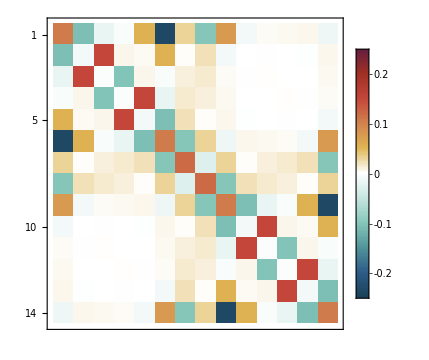

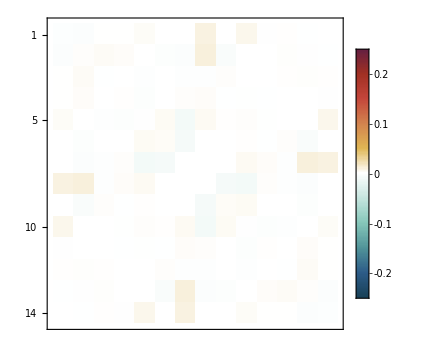

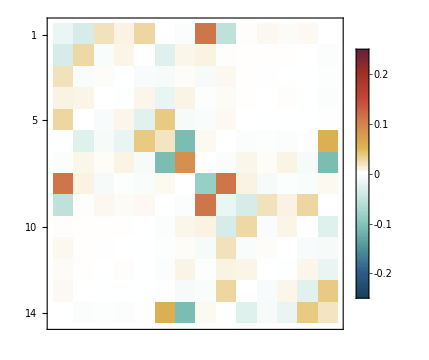

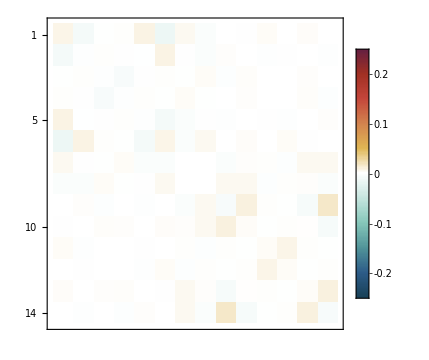

```mathematica
prettyPlot[-VIrrReps[[1]],symmetricCF[0.25],-0.25,0.25]
prettyPlot[-VIrrReps[[2]],symmetricCF[0.25],-0.25,0.25]
prettyPlot[-VIrrReps[[7]],symmetricCF[0.25],-0.25,0.25]
prettyPlot[-VIrrReps[[8]],symmetricCF[0.25],-0.25,0.25]
```

### Define the Symmetry Adapted Linear Combination (SALC) of atomic orbitals that obey the symmetry for pz orbitals on the anthracene nuclei

Projecting out the SALCs, then removing duplicates (including ones that differ by a sign) and zeros, we obtain 14 unique SALCs

```mathematica
SALCs=Join[Table[(Sum[χAu[[i]]*R[[i]],{i,1,8}]).Table[If[j==s,1,0],{j,1,14}],{s,1,14}]/8,
Table[(Sum[χB1u[[i]]*R[[i]],{i,1,8}]).Table[If[j==s,1,0],{j,1,14}],{s,1,14}]/8,
Table[(Sum[χB2g[[i]]*R[[i]],{i,1,8}]).Table[If[j==s,1,0],{j,1,14}],{s,1,14}]/8,
Table[(Sum[χB3g[[i]]*R[[i]],{i,1,8}]).Table[If[j==s,1,0],{j,1,14}],{s,1,14}]/8];
temp={};
For[i=1,i<Length[SALCs],i=i+1,If[MemberQ[temp,SALCs[[i]]]||MemberQ[temp,-SALCs[[i]]],None,AppendTo[temp,SALCs[[i]]]]]
SALCs=Join[temp[[;;3]],temp[[5;;]]];
SALCs=Table[Normalize[SALCs[[i]]],{i,1,14}];
```

## Huckel Theory

To get a more quantitative understanding of the perturbation, we perform some symbolic manipulations on a toy problem

### Define the Huckel Anthracene Hamiltonian

```mathematica
HuckelHBenzene[α_,β_]:=α*IdentityMatrix[6]+myDiag[Table[β,{i,1,5}],1]+myDiag[{β},5];
HuckelHAnthracene[α_,β_]:=BlockDiagonalMatrix[{HuckelHBenzene[α,β],{{α,0},{0,α}},HuckelHBenzene[α,β]}]+addElement[14,β,6,7]+addElement[14,β,7,14]+addElement[14,β,1,8]+addElement[14,β,8,9];
```

The effect of the SALCs on the HuckelHAnthracene Hamiltonian is to make it block diagonal based on the symmetry of the orbitals {{Au, ..., ..., ...}. {..., B1u, ..., ...}, {..., ..., B2g, ...}, {..., ..., ..., B3g}}

```mathematica
Simplify[SALCs.HuckelHAnthracene[α,β].Transpose[SALCs]]//MatrixForm
```

(α-β | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
β | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | β | α-β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α+β | β | 0 | √2 β | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | β | α | β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | β | α+β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 β | 0 | 0 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | α+β | β | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α+β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α-β | β | 0 | -√2 β
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α | β | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | β | α-β | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2 β | 0 | 0 | α)

The HOMO has B3g symmetry and the LUMO has B1u symmetry

### A1g perturbations

We define a matrix were we allow a select few on-atom energies and bond energies to be chosen via function keys . δα1 corresponds to the atoms 1, 6, 9, and 14. Notably, these atoms also experience an intrinsically slightly different chemical environment by virtue of not being connected to a hydrogen atom. δα2 encodes the differences of 7,8 that arise based on the presence of the silicon. The other parameters encode the behaviour upon bending . δβ1 gives the change in the bonds between 1-2, 3-4, and 5-6. This value is about the same and opposite of the bonds between 2-3 and 4-5 given by δβ2. Finally, the bond between 1-6 and 9-14 is modified by δβ3. While δβ4 handles the other bond energy changes within the center ring . I find in the bent anthracene case that δβ1 is a positive number (making the bond energy less negative) and δβ3 is a larger positive number

```mathematica
anthracene[α_,β_,δα1_,δα2_,δβ1_,δβ2_,δβ3_,δβ4_]=HuckelHAnthracene[α,β]+addElement[14,δα1,1,1]+addElement[14,δα1,6,6]+addElement[14,δα1,14,14]+addElement[14,δα1,9,9]+addElement[14,δα2,7,7]+addElement[14,δα2,8,8]+myDiag[Table[If[Mod[i,2]!=0&&i!=7&&i!=8 &&i!=6,δβ1,0],{i,1,13}],1]+myDiag[Table[If[Mod[i,2]==0&&i!=7&&i!=8 &&i!=6,δβ2,0],{i,1,13}],1]+addElement[14,δβ3,1,6]+addElement[14,δβ3,9,14]+addElement[14,δβ4,6,7]+addElement[14,δβ4,7,14]+addElement[14,δβ4,1,8]+addElement[14,δβ4,8,9];
```

Changing to the SALC basis

```mathematica
salcAnthracene[α_,β_,δα1_,δα2_,δβ1_,δβ2_,δβ3_,δβ4_]:=Simplify[SALCs.anthracene[α,β,δα1,δα2,δβ1,δβ2,δβ3,δβ4].Transpose[SALCs]];
Vperturb[δα1_,δα2_,δβ1_,δβ2_,δβ3_,δβ4_]:=FullSimplify[salcAnthracene[α,β,δα1,δα2,δβ1,δβ2,δβ3,δβ4]-salcAnthracene[α,β,0,0,0,0,0,0]];
Vperturb[δα1,δα2,δβ1,δβ2,δβ3,δβ4]//MatrixForm
```

(δα1-δβ3 | δβ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
δβ1 | 0 | δβ2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | δβ2 | -δβ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | δα1+δβ3 | δβ1 | 0 | √2 δβ4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | δβ1 | 0 | δβ2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | δβ2 | δβ1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √2 δβ4 | 0 | 0 | δα2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | δα1+δβ3 | δβ1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | δβ1 | 0 | δβ2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | δβ2 | δβ1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | δα1-δβ3 | δβ1 | 0 | -√2 δβ4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | δβ1 | 0 | δβ2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | δβ2 | -δβ1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2 δβ4 | 0 | 0 | δα2)

We can define the eigenvalues and eigenvectors of each block in the following way

```mathematica
{Esalc01,Usalc01}=Eigensystem[salcAnthracene[α,β,0,0,0,0,0,0,0][[;;3,;;3]]];
{Esalc02,Usalc02}=Eigensystem[salcAnthracene[α,β,0,0,0,0,0,0,0][[4;;7,4;;7]]];
{Esalc03,Usalc03}=Eigensystem[salcAnthracene[α,β,0,0,0,0,0,0,0][[8;;10,8;;10]]];
{Esalc04,Usalc04}=Eigensystem[salcAnthracene[α,β,0,0,0,0,0,0,0][[11;;,11;;]]];
```

And combine them to form the matrix that will block diagonalize the Hamiltonian in the standard sense

```mathematica
Usalc0=Normal[BlockDiagonalMatrix[{Usalc01,Usalc02,Usalc03,Usalc04}]];
For[i=1,i<=14,i=i+1,Usalc0[[i,;;]]=Normalize[Usalc0[[i,;;]]];]
N[FullSimplify[Usalc0.salcAnthracene[-1,-1,0,0,0,0,0,0].Transpose[Usalc0]]]//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.414214 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.585786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2.41421 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -3.41421 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -3. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.414214 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.41421 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2.41421 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.41421)

```mathematica
(* HOMO *)
FullSimplify[Usalc0[[14,;;]].salcAnthracene[α,β,0,0,0,0,0,0].Usalc0[[14,;;]]]
(* LUMO *)
FullSimplify[Usalc0[[5,;;]].salcAnthracene[α,β,0,0,0,0,0,0].Usalc0[[5,;;]]]
```

α+(-1+√2) β

α+β-√2 β

```mathematica
FullSimplify[Chop[Usalc0[[14,;;]].salcAnthracene[0,0,0,0,δβ1,δβ2,δβ3,δβ4].Transpose[Usalc0[[14,;;]]]]]
FullSimplify[-Chop[Usalc0[[5,;;]].salcAnthracene[0,0,0,0,δβ1,δβ2,δβ3,δβ4].Transpose[Usalc0[[5,;;]]]]]
```

1/28 ((-16+3 √2) δβ1+(4+8 √2) δβ2-8 δβ3+5 √2 δβ3-8 δβ4+12 √2 δβ4)

1/28 ((-16+3 √2) δβ1+(4+8 √2) δβ2-8 δβ3+5 √2 δβ3-8 δβ4+12 √2 δβ4)

```mathematica
FullSimplify[Chop[Usalc0[[14,;;]].salcAnthracene[0,0,δα1,δα2,0,0,0,0].Transpose[Usalc0[[14,;;]]]]]
FullSimplify[Chop[Usalc0[[5,;;]].salcAnthracene[0,0,δα1,δα2,0,0,0,0].Transpose[Usalc0[[5,;;]]]]]
```

1/28 (4+√2) ((3-2 √2) δα1+2 δα2)

1/28 (4+√2) ((3-2 √2) δα1+2 δα2)

Using the values of α = -2.90, β = -3.20 we have the following eigenvalues in the un-perturbed system on the left and then the bond energy changes and the on-site energy changes moving to the right

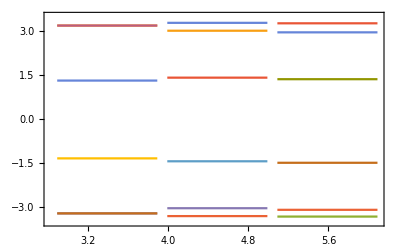

```mathematica
spectrum[Join[makeLines[Eigenvalues[salcAnthracene[-2.90,-3.2,0,0,0,0,0,0]],0],makeLines[Eigenvalues[salcAnthracene[-2.90,-3.2,0,0,0.1,-0.15,0.24,0.1]],1.1],makeLines[Eigenvalues[salcAnthracene[-2.90,-3.2,-0.1,-0.12,0.1,-0.15,0.24,0.1]],2.2]],-2.89,{-3.5,3.5}]
```

```mathematica
Sort[Eigenvalues[salcAnthracene[-2.90,-3.2,0,0,0,0,0,0]]]
%[[8]]-%[[7]]
```

{-10.6255,-9.3,-7.42548,-7.42548,-6.1,-6.1,-4.22548,-1.57452,0.3,0.3,1.62548,1.62548,3.5,4.82548}

2.65097

```mathematica
Sort[Eigenvalues[salcAnthracene[-2.90,-3.2,0,0,0.1,-0.15,0.24,0.1]]]
%[[8]]-%[[7]]
```

{-10.3819,-9.22866,-7.39971,-7.39679,-6.19254,-5.92388,-4.32478,-1.47522,0.123876,0.392538,1.59679,1.59971,3.42866,4.58185}

2.84955

```mathematica
2.84955-2.65097
```

0.19858

## Geometry Descriptions

Gaussian outputs the standard orientation of each molecule as the following points (in Å)

```mathematica
planarStandardOrientation={{0.000007,-1.405952,-0.031620},{-1.215986,-0.707789,-0.021872},{ 1.216589,-0.707757,-0.022523},{-1.216876, 0.709016,-0.022358},{-0.000042, 1.407422,-0.031008},{ 1.216063, 0.708866,-0.021735},{ 2.436580,-1.402235,-0.001184},{3.643980,-0.699053, 0.030012},{3.643899, 0.697923 ,0.030845},{ 2.436901, 1.402557, 0.000512},{-2.435657,-1.402436, 0.000802},{-3.643162,-0.699885, 0.031057},{-3.644563, 0.697665 ,0.029678},{-2.437649, 1.402574,-0.001341},{-2.455057,-2.485917, 0.005044},{-4.580899,-1.240433, 0.059313},{-4.583226, 1.235663 ,0.056481},{-2.459214, 2.486154, 0.001055},{ 0.000363,-2.490895,-0.030246},{ 2.457439, 2.486110, 0.003987},{4.582424, 1.236984, 0.059302},{2.456401,-2.485799, 0.001025}, {4.581572,-1.239110, 0.056946},{-0.000299, 2.491744,-0.028495}};
bentStandardOrientation={{0.003909,-1.386121,-0.212101},{-1.210358,-0.703665,-0.144058},{ 1.211926,-0.691853,-0.167177},{-1.213969, 0.744744,-0.189345},{-0.007007, 1.491335,-0.316201},{ 1.209397, 0.760865,-0.167429},{ 2.445383,-1.399071,-0.039951},{ 3.627842,-0.739729, 0.179876},{3.623167, 0.674086, 0.273760},{ 2.460023, 1.376642, 0.082277},{-2.437403,-1.408471, 0.028669},{-3.619282,-0.741020, 0.234674},{-3.625656, 0.674596, 0.239256},{-2.468446, 1.370459,-0.005835},{-2.403751,-2.499602, 0.039612},{-4.545442,-1.291099, 0.402971},{-4.556336, 1.215878, 0.415357},{-2.481862, 2.458522,-0.023538},{0.009443,-2.478829,-0.214432},{ 2.476473, 2.455735, 0.180991},{ 4.547724, 1.211807, 0.490543},{ 2.413486,-2.489925,-0.075642},{4.558284,-1.293911, 0.306623},{-0.015171, 2.574638,-0.300964}};
```

Relabeling the carbons to the desired scheme (ignoring the labeling of the hydrogen atoms)

```mathematica
planarStandardOrientation=planarStandardOrientation[[Join[s1,{15,16,17,18,19,20,21,22,23,24}]]];
bentStandardOrientation=bentStandardOrientation[[Join[s1,{15,16,17,18,19,20,21,22,23,24}]]];
```

### Bond Lengths

The distances between atoms are then the following matrices

```mathematica
planarDistanceMatrix=Table[Sqrt[Total[(planarStandardOrientation[[i]]-planarStandardOrientation[[j]])^2]],{i,1,24},{j,1,24}];
bentDistanceMatrix=Table[Sqrt[Total[(bentStandardOrientation[[i]]-bentStandardOrientation[[j]])^2]],{i,1,24},{j,1,24}];
```

And the changes in bond lengths (restricting to nearest neighbors only) can be visualized as

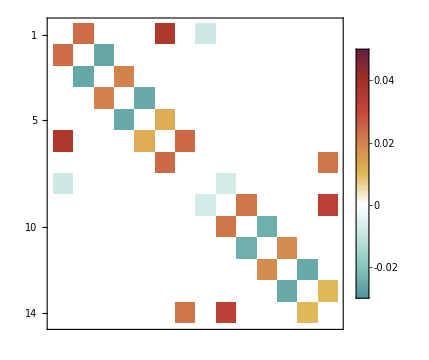

```mathematica
prettyPlot[Table[If[connectivityMatrix[[i,j]]==1,bentDistanceMatrix[[i,j]]-planarDistanceMatrix[[i,j]],0],{i,1,14},{j,1,14}],symmetricCF[0.05],-0.03,0.05]
```

### Bond Length vs Coupling

Most corrections to tight - binding models have a correction that depends exponentially on the distance between atoms . Therefore, as the distances change, we expect to see an exponential change of the coupling strength (although, it will likely look linear on the scale we are working on). Because the couplings between nearest neighbors are negative, evaluating bent - planar yields positive values if the planar coupling was stronger and negative values if the bent coupling was stronger. To avoid confusion, we evaluate |bent| - |planar|, so that if the coupling increased in the bent case the result is also positive and if the coupling decreased, the result is negative. The total change in coupling strength between nearest neighbors is given by the elements of

```mathematica
deltaCoupling=Flatten[UpperTriangularize[Table[If[connectivityMatrix[[i,j]]==1,(Abs[bentMatrixBD[[i,j]]]-Abs[planarMatrix[[i,j]]])*1000,0],{i,1,14},{j,1,14}]]]/.{0.->Nothing,0->Nothing}
```

{-5.7641,-9.27827,0.519912,5.37749,-4.02085,5.66896,-2.861,-8.24722,-7.30954,0.175676,-4.84252,-8.11104,5.13365,-3.52305,5.79673,-2.3925}

The changes in bond lengths are then

```mathematica
deltaDistance=Flatten[UpperTriangularize[Table[If[connectivityMatrix[[i,j]]==1,(bentDistanceMatrix[[i,j]]-planarDistanceMatrix[[i,j]])*100,0],{i,1,14},{j,1,14}]]]/.{0.->Nothing,0->Nothing}
```

{2.35308,3.60969,-0.868845,-2.59961,1.99602,-2.56725,1.18603,2.41699,2.18243,-0.763209,2.17645,3.2316,-2.44728,1.80864,-2.56533,0.963677}

And plotting them gives

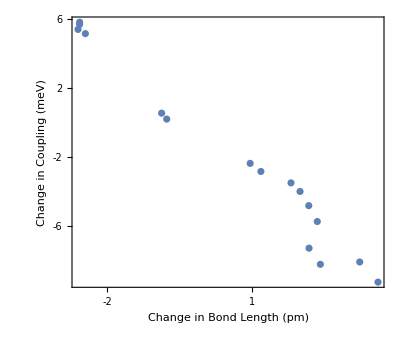

```mathematica
ListPlot[Transpose[{deltaDistance,deltaCoupling}],Axes->None,
Frame->True,FrameLabel->{"Change in Bond Length (pm)","Change in Coupling (meV)"},FrameTicks->{{Table[x,{x,-10,10,2}],None},{Table[x,{x,-5,5}],None}},AspectRatio->0.85]
```

### Tetrahedrality Order Parameter

#### Planar Anthracene

Silicon tetrahedrality

In order of: the silicon involved in bonding with anthracene, the 3 silicons in the lattice, and then the carbon in the anthracene

```mathematica
atoms={{11.49922, 6.66105, 18.83035},{9.61138, 5.53176, 18.00713},{11.50441, 8.83890, 17.97066},{13.40483, 5.53255, 18.03062},{11.47247, 6.62224, 20.91452}};
1-(3/8)*Sum[((atoms[[j+1]]-atoms[[1]]).(atoms[[k+1]]-atoms[[1]])/(Norm[atoms[[j+1]]-atoms[[1]]]*Norm[atoms[[k+1]]-atoms[[1]]])+1/3)^2,{j,1,3},{k,j+1,4}] (*The expression in Joel's paper*)
```

0.998468

Carbon tetrahedrality

In order of: the carbon bonded to the silicon surface, the two carbons bound to it, the silicon in the surface. We generate a VSEPR style ghost hydrogen an appropriate distance from the central carbon as far away from the others as we can get.

```mathematica
atoms={{11.47247, 6.62224, 20.91452},{10.46234, 6.02645, 21.74743},{12.55524, 7.22572, 21.63188},{11.49922, 6.66105, 18.83035}};
distanceCH=1.09;
ghostH={x,y,z}/.Maximize[{Sum[Norm[atoms[[i]]-{x,y,z}],{i,2,4}],Norm[atoms[[1]]-{x,y,z}]==distanceCH},{x,y,z}][[2]]
AppendTo[atoms,ghostH];
1-(3/8)*Sum[((atoms[[j+1]]-atoms[[1]]).(atoms[[k+1]]-atoms[[1]])/(Norm[atoms[[j+1]]-atoms[[1]]]*Norm[atoms[[k+1]]-atoms[[1]]])+1/3)^2,{j,1,3},{k,j+1,4}]
```

{11.9144,5.62616,20.9398}

0.830476

#### Bent Anthracene

Silicon tetrahedrality

In order of : the silicon involved in bonding with anthracene, the 3 silicons in the lattice, and then the carbon in the anthracene

```mathematica
atoms={{11.46731, 6.72088, 19.13517},{9.62832, 5.58712, 18.11017},{11.48479, 8.86756, 18.10766},{13.38063, 5.61853, 18.17296},{11.30092, 6.62765, 21.07611}};
1-(3/8)*Sum[((atoms[[j+1]]-atoms[[1]]).(atoms[[k+1]]-atoms[[1]])/(Norm[atoms[[j+1]]-atoms[[1]]]*Norm[atoms[[k+1]]-atoms[[1]]])+1/3)^2,{j,1,3},{k,j+1,4}]
```

0.977115

Carbon tetrahedrality

In order of : the carbon bonded to the silicon surface, the two carbons bound to it, the silicon in the surface . We generate a VSEPR style ghost hydrogen an appropriate distance from the central carbon as far away from the others as we can get .

```mathematica
atoms={{11.30092, 6.62765, 21.07611},{11.46731, 6.72088, 19.13517},{12.35695, 6.15290 ,21.89704},{10.08942, 6.94329, 21.75231}};
ghostH={x,y,z}/.Maximize[{Sum[Norm[atoms[[i]]-{x,y,z}],{i,2,4}],Norm[atoms[[1]]-{x,y,z}]==distanceCH},{x,y,z}][[2]]
AppendTo[atoms,ghostH];
1-(3/8)*Sum[((atoms[[j+1]]-atoms[[1]]).(atoms[[k+1]]-atoms[[1]])/(Norm[atoms[[j+1]]-atoms[[1]]]*Norm[atoms[[k+1]]-atoms[[1]]])+1/3)^2,{j,1,3},{k,j+1,4}]
```

{11.6426,7.65137,21.2289}

0.854968